```mathematica
(*finally fixed by changing file format,yay*)
(*set directory and import database file start from 3rd colomn *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
myImport = Import["train.xlsx",{"Data",1}] [[3;;]];
```

```mathematica
(*data transformation turn database tuple into the list*)
```

```mathematica
myData=Thread[myImport[[1;;,1;;-2]]->myImport[[1;;,-1]]];
```

```mathematica
(*extract 80% sample data from mydata as trainning,the remainning 20% as testing the accuracy *)
```

```mathematica
sampleSize=IntegerPart[Length@myData*0.8];
myDataTrain=RandomSample[myData,sampleSize];
myDataTest=Complement[myData,myDataTrain];
```

```mathematica
(*automatic classify trainning*)
myClassify=Classify[myDataTrain];
```

```mathematica
(*accuracy test*)
```

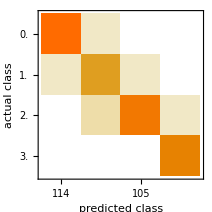
Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 400
Accuracy | (97.30.8) %
Accuracy baseline | (28.52.3) %
Geometric mean of probabilities | 0.815 ± 0.0084
Mean cross entropy | 0.205 ± 0.01
Single evaluation time | 2.04 ms/example
Batch evaluation speed | 80.6 examples/ms
-Graphics- |

```mathematica
myAccuracyDiag=ClassifierMeasurements[myClassify,myDataTest];
myAccuracyDiag["Report"]
```

```mathematica
(*save trained classify*)
SetDirectory[NotebookDirectory[]];
DumpSave["trained_phone_price_predict.mx",myClassify];
```